```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]<>"../"];
Needs["ThinLayer`","ThinLayer.m"]
```

## Rock physics model

```mathematica
Module[{λ=10.6957 ,μ=21.9734 ,ρ2=2.15,ϕ=.28,kf=2.4,ϵ=0.02,ϵf=0.03,α=10^-5,τ=2. 10^-5,cijPorous,cijFractured,
thick=.005,is=600,fs=20},
cijPorous[f_]:=tlVTISquirtModuli[ϵ,0,α,τ,2Pi f,0][λ,μ,ρ2,ϕ,kf];
cijFractured[f_,lenrat_]:=tlVTISquirtModuli[ϵ,ϵf,α,τ,2Pi f,lenrat][λ,μ,ρ2,ϕ,kf];

vel={{
Show[
Plot[Evaluate@Re[{√((#[[1]])/(#[[5]])),√((#[[3]])/(#[[5]]))}&@cijPorous[10^f]],{f,0,5},PlotRange->{Full,{2.78,3.51}},ImageSize->is,Frame->True,PlotStyle->(Directive[#,Thickness[thick],Black]&/@{None,Dashed}),GridLines->Automatic,FrameLabel->{{"V, km/s",None},{"Log f","qP Velocity dispersion"}},LabelStyle->Directive[Black,Bold,FontSize->fs]],
Plot[Evaluate@Re[{√((#[[1]])/(#[[5]])),√((#[[3]])/(#[[5]]))}&@cijFractured[10^f,100]],{f,0,5},PlotRange->{Full,Full},PlotStyle->(Directive[#,Red,Thickness[thick]]&/@{None,Dashed})],
Plot[Evaluate@Re[{√((#[[1]])/(#[[5]])),√((#[[3]])/(#[[5]]))}&@cijFractured[10^f,200]],{f,0,5},PlotRange->{Full,Full},PlotStyle->(Directive[#,Cyan,Thickness[thick]]&/@{None,Dashed})],
Plot[Evaluate@Re[{√((#[[1]])/(#[[5]])),√((#[[3]])/(#[[5]]))}&@cijFractured[10^f,300]],{f,0,5},PlotRange->{Full,Full},PlotStyle->(Directive[#,Magenta,Thickness[thick]]&/@{None,Dashed})]
],
Show[
Plot[Evaluate@Re[√((#[[4]])/(#[[5]]))&@cijPorous[10^f]],{f,0,5},PlotRange->{Full,{1.82,2.06}},ImageSize->is,Frame->True,PlotStyle->(Directive[#,Thick]&/@{Black}),GridLines->Automatic,FrameLabel->{{"V, km/s",None},{"Log f","qS Velocity dispersion"}},LabelStyle->Directive[Black,Bold,FontSize->fs]],
Plot[Evaluate@Re[√((#[[4]])/(#[[5]]))&@cijFractured[10^f,100]],{f,0,5},PlotRange->{Full,Full},PlotStyle->(Directive[#,Red,Thickness[thick]]&/@{Dashed})],
Plot[Evaluate@Re[√((#[[4]])/(#[[5]]))&@cijFractured[10^f,200]],{f,0,5},PlotRange->{Full,Full},PlotStyle->(Directive[#,Cyan,Thickness[thick]]&/@{Dashed})],
Plot[Evaluate@Re[√((#[[4]])/(#[[5]]))&@cijFractured[10^f,500]],{f,0,5},PlotRange->{Full,Full},PlotStyle->(Directive[#,Magenta,Thickness[thick]]&/@{Dashed})]
]}};

Q={{
Show[
Plot[Evaluate[{(Im@#[[1]])/(Re@#[[1]]),(Im@#[[3]])/(Re@#[[3]])}&@cijPorous[10^f]],{f,0,5},PlotRange->{Full,{0,.22}},ImageSize->is,Frame->True,PlotStyle->(Directive[#,Black,Thickness[thick]]&/@{None,Dashed}),GridLines->Automatic,FrameLabel->{{"1/Q",None},{"Log f","qP attenuation"}},LabelStyle->Directive[Black,Bold,FontSize->fs]],
Plot[Evaluate[{(Im@#[[1]])/(Re@#[[1]]),(Im@#[[3]])/(Re@#[[3]])}&@cijFractured[10^f,100]],{f,0,5},PlotRange->{Full,Full},PlotStyle->(Directive[#,Red,Thickness[thick]]&/@{None,Dashed})],
Plot[Evaluate[{(Im@#[[1]])/(Re@#[[1]]),(Im@#[[3]])/(Re@#[[3]])}&@cijFractured[10^f,200]],{f,0,5},PlotRange->{Full,Full},PlotStyle->(Directive[#,Cyan,Thickness[thick]]&/@{None,Dashed})],
Plot[Evaluate[{(Im@#[[1]])/(Re@#[[1]]),(Im@#[[3]])/(Re@#[[3]])}&@cijFractured[10^f,300]],{f,0,5},PlotRange->{Full,Full},PlotStyle->(Directive[#,Magenta,Thickness[thick]]&/@{None,Dashed})]
],
Show[
Plot[Evaluate[(Im@#[[4]])/(Re@#[[4]])&@cijPorous[10^f]],{f,0,5},PlotRange->{Full,{0,.02}},ImageSize->is,Frame->True,PlotStyle->(Directive[#,Thickness[thick]]&/@{Black}),GridLines->Automatic,FrameLabel->{{"1/Q",None},{"Log f","qS attenuation"}},LabelStyle->Directive[Black,Bold,FontSize->fs]],
Plot[Evaluate[(Im@#[[4]])/(Re@#[[4]])&@cijFractured[10^f,100]],{f,0,5},PlotRange->{Full,Full},PlotStyle->(Directive[#,Red,Thickness[thick]]&/@{None})],
Plot[Evaluate[(Im@#[[4]])/(Re@#[[4]])&@cijFractured[10^f,200]],{f,0,5},PlotRange->{Full,Full},PlotStyle->(Directive[#,Cyan,Thickness[thick]]&/@{None})],
Plot[Evaluate[(Im@#[[4]])/(Re@#[[4]])&@cijFractured[10^f,300]],{f,0,5},PlotRange->{Full,Full},PlotStyle->(Directive[#,Magenta,Thickness[thick]]&/@{None})]
]}};
]
```

```mathematica
Table[Export[NotebookDirectory[]<>"../../../../Publications_and_conferences/Conferences/EAGE-2019/Abstract/Fig/vel-"<>Switch[i,1,"P",2,"S"]<>".png",vel[[1,i]],ImageResolution->1000],{i,2}];
Table[Export[NotebookDirectory[]<>"../../../../Publications_and_conferences/Conferences/EAGE-2019/Abstract/Fig/q-"<>Switch[i,1,"P",2,"S"]<>".png",Q[[1,i]],ImageResolution->1000],{i,2}]
```

{/Users/ymac/Dropbox/Study_etc/NTNU/Anisotropy/Mathematica/PETROMAKS/PM2-codes/EAGE'19/../../../../Publications_and_conferences/Conferences/EAGE-2019/Abstract/Fig/q-P.png,/Users/ymac/Dropbox/Study_etc/NTNU/Anisotropy/Mathematica/PETROMAKS/PM2-codes/EAGE'19/../../../../Publications_and_conferences/Conferences/EAGE-2019/Abstract/Fig/q-S.png}

```mathematica
Table[Export[NotebookDirectory[]<>"../../../../Publications_and_conferences/Conferences/EAGE-2019/Abstract/Fig/vel-"<>Switch[i,1,"P",2,"S"]<>".pdf",vel[[1,i]]],{i,2}];
Table[Export[NotebookDirectory[]<>"../../../../Publications_and_conferences/Conferences/EAGE-2019/Abstract/Fig/q-"<>Switch[i,1,"P",2,"S"]<>".pdf",Q[[1,i]]],{i,2}]
```

{C:\Users\yuriyi\Dropbox\Study_etc\NTNU\Anisotropy\Mathematica\PETROMAKS\PM2-codes\EAGE'19\../../../../Publications_and_conferences/Conferences/EAGE-2019/Abstract/Fig/q-P.pdf,C:\Users\yuriyi\Dropbox\Study_etc\NTNU\Anisotropy\Mathematica\PETROMAKS\PM2-codes\EAGE'19\../../../../Publications_and_conferences/Conferences/EAGE-2019/Abstract/Fig/q-S.pdf}

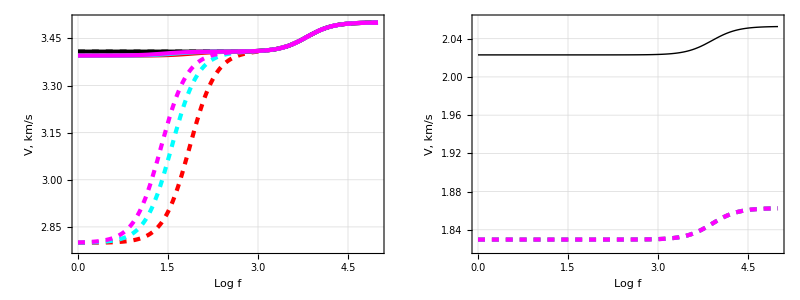

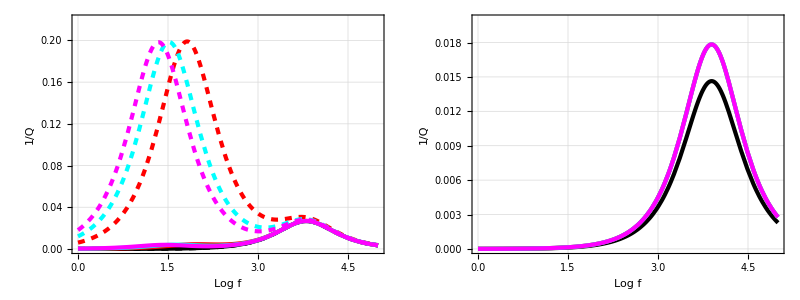

```mathematica
vel//TableForm
Q//TableForm
```

## Shot gathers

#### d = 0.5 km; L = 100/200/300

```mathematica
x=Range[.1,2,.01];
L=Range[100,300,100];
```

```mathematica
(* MODEL INITIALIZATION *)
setlayer[ω_,lenrat_]:=Module[
{λ=10.6957 ,μ=21.9734 ,ρ2=2.15,ϕ=.28,kf=2.4,ϵ=0.02,ϵf=0.03,α=10^-5,τ=2. 10^-5,cijPorous,cijFractured},
cijPorous=tlVTISquirtModuli[ϵ,0,α,τ,ω,0][λ,μ,ρ2,ϕ,kf];
cijFractured=tlVTISquirtModuli[ϵ,ϵf,α,τ,ω,lenrat][λ,μ,ρ2,ϕ,kf];
tlSetLayer[1,cijPorous];
tlSetLayer[2,cijFractured];
]
```

```mathematica
setlayer[2Pi 25,100]
```

```mathematica
{freqvec,L100,pI,ωI,layers,depth}=Uncompress@Import[NotebookDirectory[]<>"./l100n0d500.mc","String"];
{freqvec,L200,pI,ωI,layers,depth}=Uncompress@Import[NotebookDirectory[]<>"./l200n0d500.mc","String"];
{freqvec,L300,pI,ωI,layers,depth}=Uncompress@Import[NotebookDirectory[]<>"./l300n0d500.mc","String"];

{freqvec,L100NewQ,pI,ωI,layers,depth}=Uncompress@Import[NotebookDirectory[]<>"./l100n0d500_NewQ.mc","String"];
{freqvec,L200NewQ,pI,ωI,layers,depth}=Uncompress@Import[NotebookDirectory[]<>"./l200n0d500_NewQ.mc","String"];
{freqvec,L300NewQ,pI,ωI,layers,depth}=Uncompress@Import[NotebookDirectory[]<>"./l300n0d500_NewQ.mc","String"];
```

{data, t} written to l100Z

{data, t} written to l100ZNewQ

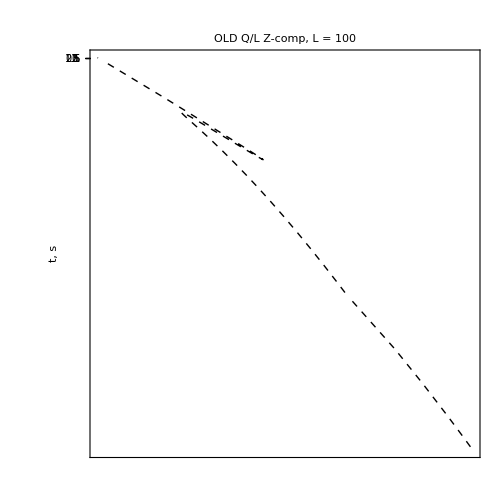
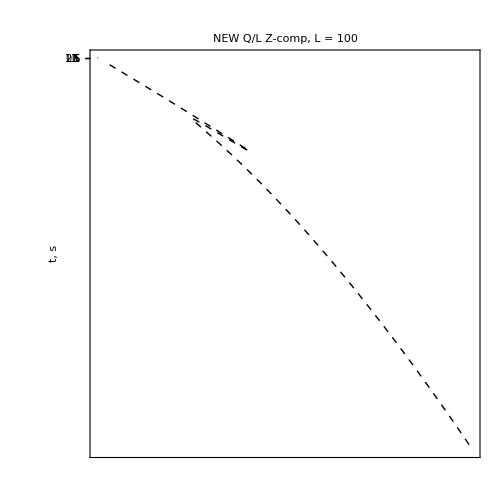
-Graphics--Graphics--Graphics- | -Graphics--Graphics--Graphics-

```mathematica
{{tlPlotSeismic[ToString@Row[{"OLD Q/L Z-comp, L = ",L[[1]]}],L100[[;;,1,;;]],freqvec,x,15,Abs@ωI,layers,depth,{.4,.8},l100Z,50,2.00001,"1S2PP1P"],
tlPlotSeismic[ToString@Row[{"NEW Q/L Z-comp, L = ",L[[1]]}],L100NewQ[[;;,1,;;]],freqvec,x,15,Abs@ωI,layers,depth,{.4,.8},l100ZNewQ,50,2.00001,"1P2P3PP2P1P"]}}//TableForm
```

{data, t} written to l100R

{data, t} written to l100RNewQ

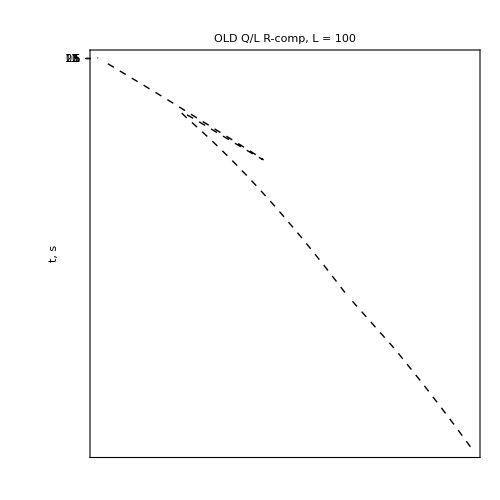
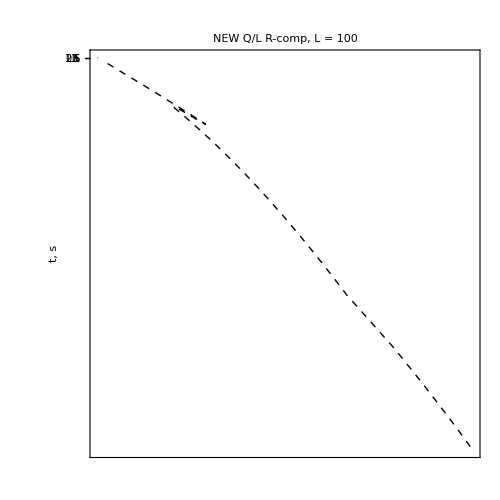
-Graphics--Graphics--Graphics- | -Graphics--Graphics--Graphics-

```mathematica
{{tlPlotSeismic[ToString@Row[{"OLD Q/L R-comp, L = ",L[[1]]}],L100[[;;,2,;;]],freqvec,x,15,Abs@ωI,layers,depth,{.4,.8},l100R,50,2.00001,"1S2PP1P"],
tlPlotSeismic[ToString@Row[{"NEW Q/L R-comp, L = ",L[[1]]}],L100NewQ[[;;,2,;;]],freqvec,x,15,Abs@ωI,layers,depth,{.4,.8},l100RNewQ,50,2.00001,"1S2PS1P"]}}//TableForm
```

## Single traces

#### d = 0.5 km; L = 100/200/300

```mathematica
With[{i=91,is=750,lim={0.4,.81}},traces1={{Show[
tlPlotTrace[L100[[;;,1,i]],freqvec,Abs@ωI,Red,50,lim,is,"OLD Q/L Z component, x = "<>ToString[x[[i]]]<>" km"],
tlPlotTrace[L200[[;;,1,i]],freqvec,Abs@ωI,Cyan,50,lim,is,None],
tlPlotTrace[L300[[;;,1,i]],freqvec,Abs@ωI,Magenta,50,lim,is,None],LabelStyle->Directive[Black,Bold,FontSize->20]],
Show[
tlPlotTrace[L100NewQ[[;;,1,i]],freqvec,Abs@ωI,Red,50,lim,is,"NEW Q/L Z component, x = "<>ToString[x[[i]]]<>" km"],
tlPlotTrace[L200NewQ[[;;,1,i]],freqvec,Abs@ωI,Cyan,50,lim,is,None],
tlPlotTrace[L300NewQ[[;;,1,i]],freqvec,Abs@ωI,Magenta,50,lim,is,None],LabelStyle->Directive[Black,Bold,FontSize->20]]}};]
```

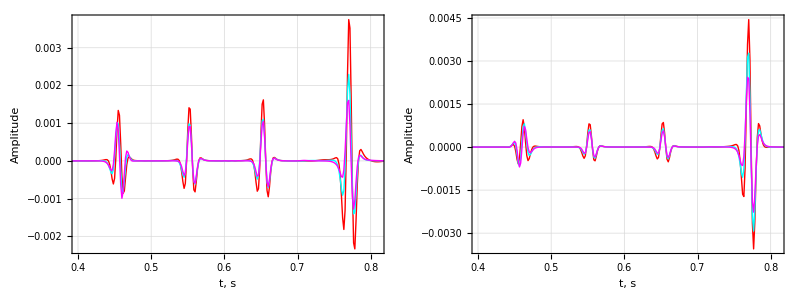

```mathematica
traces1//TableForm
```

```mathematica
With[{i=91,is=750,lim={0.4,.81}},traces2={{Show[
tlPlotTrace[L100[[;;,2,i]],freqvec,Abs@ωI,Red,50,lim,is,"OLD Q/L R component, x = "<>ToString[x[[i]]]<>" km"],
tlPlotTrace[L200[[;;,2,i]],freqvec,Abs@ωI,Cyan,50,lim,is,None],
tlPlotTrace[L300[[;;,2,i]],freqvec,Abs@ωI,Magenta,50,lim,is,None],LabelStyle->Directive[Black,Bold,FontSize->20]],
Show[
tlPlotTrace[L100NewQ[[;;,2,i]],freqvec,Abs@ωI,Red,50,lim,is,"NEW Q/L R component, x = "<>ToString[x[[i]]]<>" km"],
tlPlotTrace[L200NewQ[[;;,2,i]],freqvec,Abs@ωI,Cyan,50,lim,is,None],
tlPlotTrace[L300NewQ[[;;,2,i]],freqvec,Abs@ωI,Magenta,50,lim,is,None],LabelStyle->Directive[Black,Bold,FontSize->20]]}};]
```

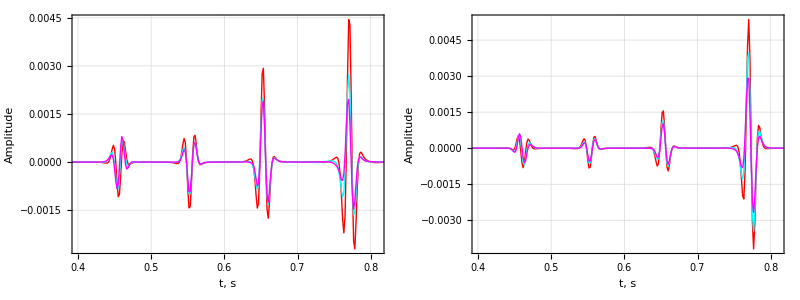

```mathematica
traces2//TableForm
```

```mathematica
Table[Export[NotebookDirectory[]<>"../../../../Publications_and_conferences/Conferences/EAGE-2019/Abstract/Fig/traces-"<>Switch[i,1,"Z",2,"R"]<>".png",traces1[[1,i]],ImageResolution->1000],{i,2}]
```

{C:\Users\yuriyi\Dropbox\Study_etc\NTNU\Anisotropy\Mathematica\PETROMAKS\PM2-codes\EAGE'19\../../../../Publications_and_conferences/Conferences/EAGE-2019/Abstract/Fig/traces-Z.png,C:\Users\yuriyi\Dropbox\Study_etc\NTNU\Anisotropy\Mathematica\PETROMAKS\PM2-codes\EAGE'19\../../../../Publications_and_conferences/Conferences/EAGE-2019/Abstract/Fig/traces-R.png}

```mathematica
Table[Export[NotebookDirectory[]<>"../../../../Publications_and_conferences/Conferences/EAGE-2019/Abstract/Fig/traces-"<>Switch[i,1,"Z",2,"R"]<>".pdf",traces1[[1,i]]],{i,2}]
```

{C:\Users\yuriyi\Dropbox\Study_etc\NTNU\Anisotropy\Mathematica\PETROMAKS\PM2-codes\EAGE'19\../../../../Publications_and_conferences/Conferences/EAGE-2019/Abstract/Fig/traces-Z.pdf,C:\Users\yuriyi\Dropbox\Study_etc\NTNU\Anisotropy\Mathematica\PETROMAKS\PM2-codes\EAGE'19\../../../../Publications_and_conferences/Conferences/EAGE-2019/Abstract/Fig/traces-R.pdf}

```mathematica
With[{i=91,is=750,lim={0.81,1.3},prv=.0004{-1,1}},traces3={{Show[
tlPlotTrace[L100[[;;,1,i]],freqvec,Abs@ωI,Red,50,lim,is,"OLD Q/L Z component, x = "<>ToString[x[[i]]]<>" km",prv],
tlPlotTrace[L200[[;;,1,i]],freqvec,Abs@ωI,Cyan,50,lim,is,None,prv],
tlPlotTrace[L300[[;;,1,i]],freqvec,Abs@ωI,Magenta,50,lim,is,None,prv],LabelStyle->Directive[Black,Bold,FontSize->20]],
Show[
tlPlotTrace[L100NewQ[[;;,1,i]],freqvec,Abs@ωI,Red,50,lim,is,"NEW Q/L Z component, x = "<>ToString[x[[i]]]<>" km",prv],
tlPlotTrace[L200NewQ[[;;,1,i]],freqvec,Abs@ωI,Cyan,50,lim,is,None,prv],
tlPlotTrace[L300NewQ[[;;,1,i]],freqvec,Abs@ωI,Magenta,50,lim,is,None,prv],LabelStyle->Directive[Black,Bold,FontSize->20]]}};]
```

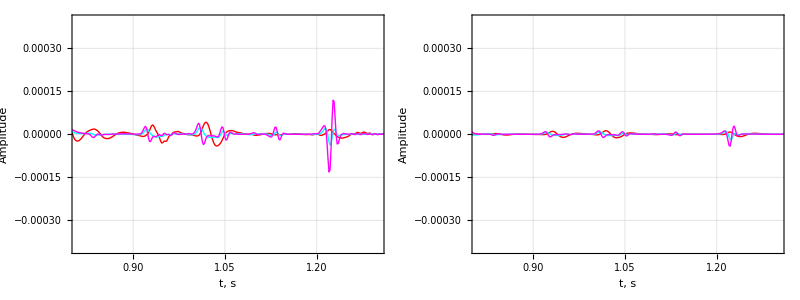

```mathematica
traces3//TableForm
```

```mathematica
With[{i=91,is=750,lim={0.81,1.3},prv=.0004{-1,1}},traces4={{Show[
tlPlotTrace[L100[[;;,2,i]],freqvec,Abs@ωI,Red,50,lim,is,"OLD Q/L R component, x = "<>ToString[x[[i]]]<>" km",prv],
tlPlotTrace[L200[[;;,2,i]],freqvec,Abs@ωI,Cyan,50,lim,is,None,prv],
tlPlotTrace[L300[[;;,2,i]],freqvec,Abs@ωI,Magenta,50,lim,is,None,prv],LabelStyle->Directive[Black,Bold,FontSize->20]],
Show[
tlPlotTrace[L100NewQ[[;;,2,i]],freqvec,Abs@ωI,Red,50,lim,is,"NEW Q/L R component, x = "<>ToString[x[[i]]]<>" km",prv],
tlPlotTrace[L200NewQ[[;;,2,i]],freqvec,Abs@ωI,Cyan,50,lim,is,None,prv],
tlPlotTrace[L300NewQ[[;;,2,i]],freqvec,Abs@ωI,Magenta,50,lim,is,None,prv],LabelStyle->Directive[Black,Bold,FontSize->20]]}};]
```

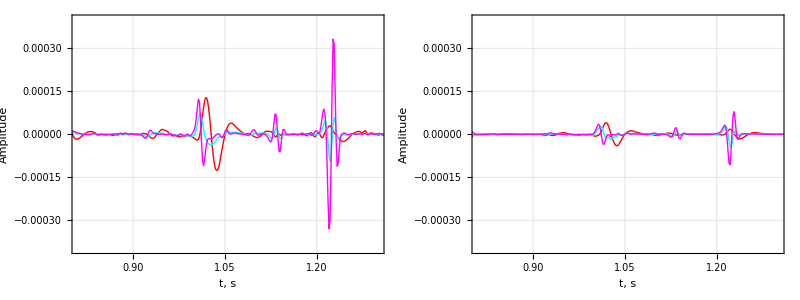

```mathematica
traces4//TableForm
```

```mathematica
Table[Export[NotebookDirectory[]<>"../../../../Publications_and_conferences/Conferences/EAGE-2019/Abstract/Fig/tracesLate-"<>Switch[i,1,"Z",2,"R"]<>".png",traces2[[1,i]],ImageResolution->1000],{i,2}]
```

{C:\Users\yuriyi\Dropbox\Study_etc\NTNU\Anisotropy\Mathematica\PETROMAKS\PM2-codes\EAGE'19\../../../../Publications_and_conferences/Conferences/EAGE-2019/Abstract/Fig/tracesLate-Z.png,C:\Users\yuriyi\Dropbox\Study_etc\NTNU\Anisotropy\Mathematica\PETROMAKS\PM2-codes\EAGE'19\../../../../Publications_and_conferences/Conferences/EAGE-2019/Abstract/Fig/tracesLate-R.png}

```mathematica
Table[Export[NotebookDirectory[]<>"../../../../Publications_and_conferences/Conferences/EAGE-2019/Abstract/Fig/tracesLate-"<>Switch[i,1,"Z",2,"R"]<>".pdf",traces2[[1,i]]],{i,2}]
```

{C:\Users\yuriyi\Dropbox\Study_etc\NTNU\Anisotropy\Mathematica\PETROMAKS\PM2-codes\EAGE'19\../../../../Publications_and_conferences/Conferences/EAGE-2019/Abstract/Fig/tracesLate-Z.pdf,C:\Users\yuriyi\Dropbox\Study_etc\NTNU\Anisotropy\Mathematica\PETROMAKS\PM2-codes\EAGE'19\../../../../Publications_and_conferences/Conferences/EAGE-2019/Abstract/Fig/tracesLate-R.pdf}

## Differences between CSG

```mathematica
With[{delta1=l100Z[[1]]-l100ZNewQ[[1]],delta2=l100R[[1]]-l100RNewQ[[1]]},
diffoldnew={{tlPlotDiff[ToString@Row[{"Z-comp, ΔNEW/OLD Q/L, L = ",100}],delta1,x,l100Z[[2]],10,{0.3,1.5},0,1/GoldenRatio],
tlPlotDiff[ToString@Row[{"R-comp, ΔNEW/OLD Q/L, L = ",100}],delta2,x,l100Z[[2]],10,{0.3,1.5},0,1/GoldenRatio]}}
]
```

{{-Graphics-,-Graphics-}}

```mathematica
With[{delta1=l100Z[[1]]-l200Z[[1]],delta2=l100R[[1]]-l200R[[1]]},
diff100200={{tlPlotDiff[ToString@Row[{"Z-comp, ΔL: ",L[[1]],", ",L[[2]]}],delta1,x,l100Z[[2]],1,{0.3,1.5},0,1/GoldenRatio],
tlPlotDiff[ToString@Row[{"R-comp, ΔL: ",L[[1]],", ",L[[2]]}],delta2,x,l100Z[[2]],1,{0.3,1.5},0,1/GoldenRatio]}}
]
```

{{-Graphics-,-Graphics-}}

```mathematica
With[{delta1=l200Z[[1]]-l300Z[[1]],delta2=l200R[[1]]-l300R[[1]]},
diff200300={{tlPlotDiff[ToString@Row[{"Z-comp, ΔL: ",L[[2]],", ",L[[3]]}],delta1,x,l100Z[[2]],1,{0.3,1.5},0,1/GoldenRatio],
tlPlotDiff[ToString@Row[{"R-comp, ΔL: ",L[[2]],", ",L[[3]]}],delta2,x,l100Z[[2]],1,{0.3,1.5},0,1/GoldenRatio]}}
]
```

{{-Graphics-,-Graphics-}}

```mathematica
Table[
Table[
Export[NotebookDirectory[]<>"../../../../Publications_and_conferences/Conferences/EAGE-2019/Abstract/Fig/diff-"<>Switch[i,1,"Z",2,"R"]<>Switch[j,1,"100300",2,"100200",3,"200300"]<>".png",Switch[j,1,diff100300,2,diff100200,3,diff200300][[1,i]],ImageResolution->1000],
{i,2}],{j,3}
]
```

{{C:\Users\yuriyi\Dropbox\Study_etc\NTNU\Anisotropy\Mathematica\PETROMAKS\PM2-codes\EAGE'19\../../../../Publications_and_conferences/Conferences/EAGE-2019/Abstract/Fig/diff-Z100300.png,C:\Users\yuriyi\Dropbox\Study_etc\NTNU\Anisotropy\Mathematica\PETROMAKS\PM2-codes\EAGE'19\../../../../Publications_and_conferences/Conferences/EAGE-2019/Abstract/Fig/diff-R100300.png},{C:\Users\yuriyi\Dropbox\Study_etc\NTNU\Anisotropy\Mathematica\PETROMAKS\PM2-codes\EAGE'19\../../../../Publications_and_conferences/Conferences/EAGE-2019/Abstract/Fig/diff-Z100200.png,C:\Users\yuriyi\Dropbox\Study_etc\NTNU\Anisotropy\Mathematica\PETROMAKS\PM2-codes\EAGE'19\../../../../Publications_and_conferences/Conferences/EAGE-2019/Abstract/Fig/diff-R100200.png},{C:\Users\yuriyi\Dropbox\Study_etc\NTNU\Anisotropy\Mathematica\PETROMAKS\PM2-codes\EAGE'19\../../../../Publications_and_conferences/Conferences/EAGE-2019/Abstract/Fig/diff-Z200300.png,C:\Users\yuriyi\Dropbox\Study_etc\NTNU\Anisotropy\Mathematica\PETROMAKS\PM2-codes\EAGE'19\../../../../Publications_and_conferences/Conferences/EAGE-2019/Abstract/Fig/diff-R200300.png}}

```mathematica
Table[
Table[
Export[NotebookDirectory[]<>"../../../../Publications_and_conferences/Conferences/EAGE-2019/Abstract/Fig/diff-"<>Switch[i,1,"Z",2,"R"]<>Switch[j,1,"100300",2,"100200",3,"200300"]<>".pdf",Switch[j,1,diff100300,2,diff100200,3,diff200300][[1,i]]],
{i,2}],{j,3}
]
```

{{C:\Users\yuriyi\Dropbox\Study_etc\NTNU\Anisotropy\Mathematica\PETROMAKS\PM2-codes\EAGE'19\../../../../Publications_and_conferences/Conferences/EAGE-2019/Abstract/Fig/diff-Z100300.pdf,C:\Users\yuriyi\Dropbox\Study_etc\NTNU\Anisotropy\Mathematica\PETROMAKS\PM2-codes\EAGE'19\../../../../Publications_and_conferences/Conferences/EAGE-2019/Abstract/Fig/diff-R100300.pdf},{C:\Users\yuriyi\Dropbox\Study_etc\NTNU\Anisotropy\Mathematica\PETROMAKS\PM2-codes\EAGE'19\../../../../Publications_and_conferences/Conferences/EAGE-2019/Abstract/Fig/diff-Z100200.pdf,C:\Users\yuriyi\Dropbox\Study_etc\NTNU\Anisotropy\Mathematica\PETROMAKS\PM2-codes\EAGE'19\../../../../Publications_and_conferences/Conferences/EAGE-2019/Abstract/Fig/diff-R100200.pdf},{C:\Users\yuriyi\Dropbox\Study_etc\NTNU\Anisotropy\Mathematica\PETROMAKS\PM2-codes\EAGE'19\../../../../Publications_and_conferences/Conferences/EAGE-2019/Abstract/Fig/diff-Z200300.pdf,C:\Users\yuriyi\Dropbox\Study_etc\NTNU\Anisotropy\Mathematica\PETROMAKS\PM2-codes\EAGE'19\../../../../Publications_and_conferences/Conferences/EAGE-2019/Abstract/Fig/diff-R200300.pdf}}

## Shot gathers: N = 25

```mathematica
{freqvec,L100N25,pI,ωI,layersN25,depthN25}=Uncompress@Import[NotebookDirectory[]<>"./l100n25d500.mc","String"];
{freqvec,L200N25,pI,ωI,layersN25,depthN25}=Uncompress@Import[NotebookDirectory[]<>"./l200n25d500.mc","String"];
{freqvec,L300N25,pI,ωI,layersN25,depthN25}=Uncompress@Import[NotebookDirectory[]<>"./l300n25d500.mc","String"];

{freqvec,L100N25NewQ,pI,ωI,layersN25,depthN25}=Uncompress@Import[NotebookDirectory[]<>"./l100n25d500_NewQ.mc","String"];
{freqvec,L200N25NewQ,pI,ωI,layersN25,depthN25}=Uncompress@Import[NotebookDirectory[]<>"./l200n25d500_NewQ.mc","String"];
{freqvec,L300N25NewQ,pI,ωI,layersN25,depthN25}=Uncompress@Import[NotebookDirectory[]<>"./l300n25d500_NewQ.mc","String"];
```

{data, t} written to l100N25Z

{data, t} written to l100N25ZNewQ

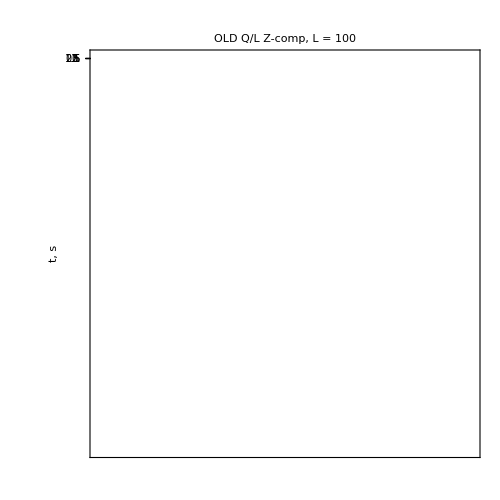
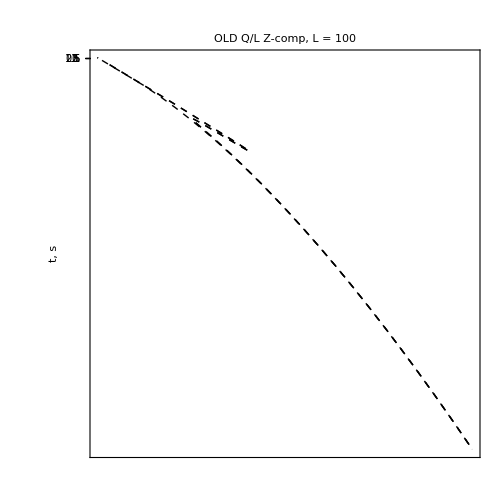
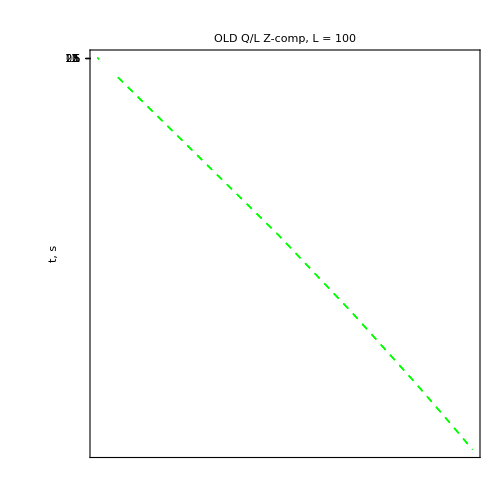
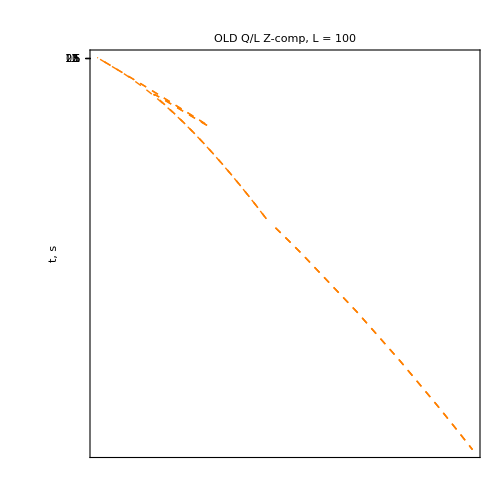
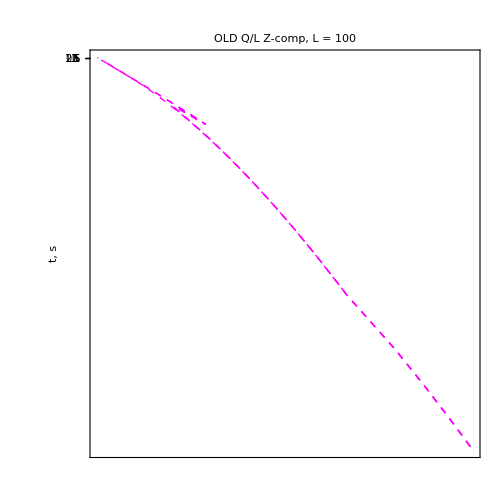
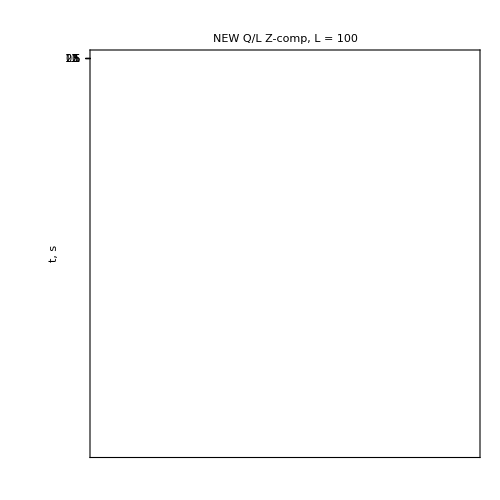
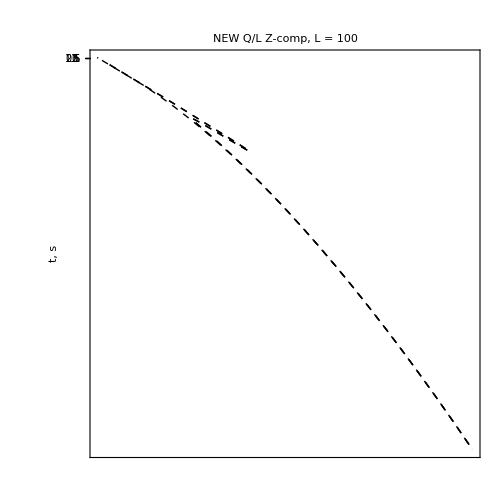
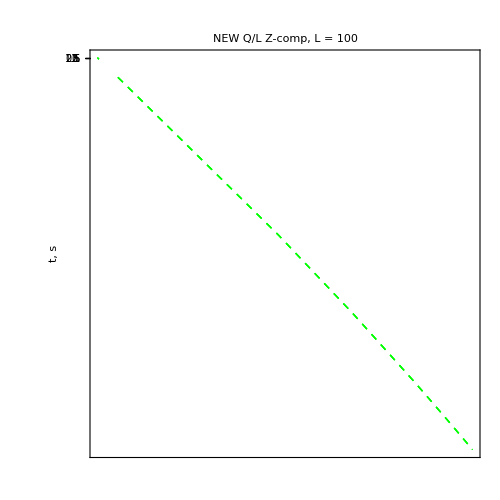
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics- | -Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
{{tlPlotSeismic[ToString@Row[{"OLD Q/L Z-comp, L = ",L[[1]]}],L100N25[[;;,1,;;]],freqvec,x,10,Abs@ωI,layers,depth,{.4,.8},l100N25Z,25,2],
tlPlotSeismic[ToString@Row[{"NEW Q/L Z-comp, L = ",L[[1]]}],L100N25NewQ[[;;,1,;;]],freqvec,x,10,Abs@ωI,layers,depth,{.4,.8},l100N25ZNewQ,25,2]}}//TableForm
```

```mathematica
With[{delta1=l100Z[[1]]-l100N25Z[[1]],delta2=l100R[[1]]-l100N25R[[1]]},
{tlPlotDiff[ToString@Row[{"Z-comp, ΔL: ",L[[1]],", ",L[[2]]}],delta1,x,l100Z[[2]],1,{0,2},0],
tlPlotDiff[ToString@Row[{"R-comp, ΔL: ",L[[1]],", ",L[[3]]}],delta2,x,l100Z[[2]],1,{0,2},0]}
]
```

{-Graphics-,-Graphics-}

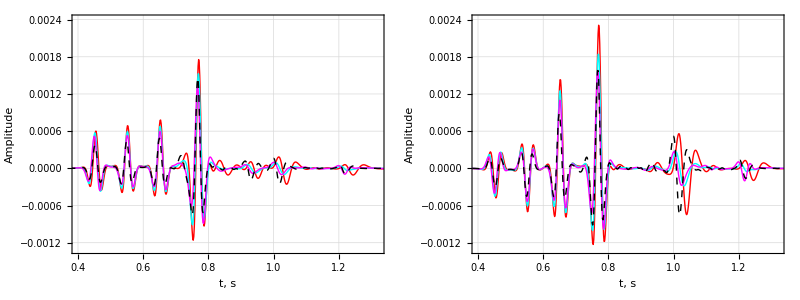

```mathematica
With[{i=91,is=750,lim={0.4,1.32},fR=20},tracesN25={{Show[
tlPlotTrace[L100[[;;,1,i]],freqvec,Abs@ωI,Red,fR,lim,is,"Z component, x = "<>ToString[x[[i]]]<>" km",{-.0013,.0024}],
tlPlotTrace[L200[[;;,1,i]],freqvec,Abs@ωI,Cyan,fR,lim,is,None],
tlPlotTrace[L300[[;;,1,i]],freqvec,Abs@ωI,Magenta,fR,lim,is,None],
tlPlotTrace[L100N25[[;;,1,i]],freqvec,Abs@ωI,{Dashed,Black},fR,lim,is,None],LabelStyle->Directive[Black,Bold,FontSize->20]],
Show[
tlPlotTrace[L100[[;;,2,i]],freqvec,Abs@ωI,Red,fR,lim,is,"R component, x = "<>ToString[x[[i]]]<>" km",{-.0013,.0024}],
tlPlotTrace[L200[[;;,2,i]],freqvec,Abs@ωI,Cyan,fR,lim,is,None],
tlPlotTrace[L300[[;;,2,i]],freqvec,Abs@ωI,Magenta,fR,lim,is,None],
tlPlotTrace[L100N25[[;;,2,i]],freqvec,Abs@ωI,{Dashed,Black},fR,lim,is,None],LabelStyle->Directive[Black,Bold,FontSize->20]]}}
];
tracesN25//TableForm
```

```mathematica
Table[Export[NotebookDirectory[]<>"../../../../Publications_and_conferences/Conferences/EAGE-2019/Abstract/Fig/traces25-"<>Switch[i,1,"Z",2,"R"]<>".png",tracesN25[[1,i]],ImageResolution->1000],{i,2}]
```

{C:\Users\yuriyi\Dropbox\Study_etc\NTNU\Anisotropy\Mathematica\PETROMAKS\PM2-codes\EAGE'19\../../../../Publications_and_conferences/Conferences/EAGE-2019/Abstract/Fig/traces25-Z.png,C:\Users\yuriyi\Dropbox\Study_etc\NTNU\Anisotropy\Mathematica\PETROMAKS\PM2-codes\EAGE'19\../../../../Publications_and_conferences/Conferences/EAGE-2019/Abstract/Fig/traces25-R.png}

```mathematica
Table[Export[NotebookDirectory[]<>"../../../../Publications_and_conferences/Conferences/EAGE-2019/Abstract/Fig/traces25-"<>Switch[i,1,"Z",2,"R"]<>".pdf",tracesN25[[1,i]]],{i,2}]
```

{C:\Users\yuriyi\Dropbox\Study_etc\NTNU\Anisotropy\Mathematica\PETROMAKS\PM2-codes\EAGE'19\../../../../Publications_and_conferences/Conferences/EAGE-2019/Abstract/Fig/traces25-Z.pdf,C:\Users\yuriyi\Dropbox\Study_etc\NTNU\Anisotropy\Mathematica\PETROMAKS\PM2-codes\EAGE'19\../../../../Publications_and_conferences/Conferences/EAGE-2019/Abstract/Fig/traces25-R.pdf}

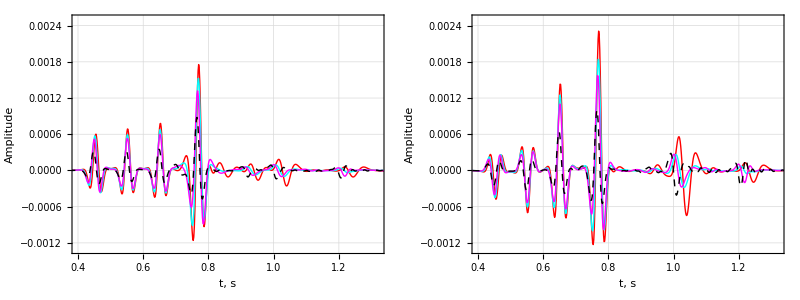

```mathematica
With[{i=91,is=750,lim={0.4,1.32}},tracesN25300={{Show[
tlPlotTrace[L100[[;;,1,i]],freqvec,Abs@ωI,Red,20,lim,is,"Z component, x = "<>ToString[x[[i]]]<>" km",{-.0013,.0025}],
tlPlotTrace[L200[[;;,1,i]],freqvec,Abs@ωI,Cyan,20,lim,is,None],
tlPlotTrace[L300[[;;,1,i]],freqvec,Abs@ωI,Magenta,20,lim,is,None],
tlPlotTrace[L300N25[[;;,1,i]],freqvec,Abs@ωI,{Dashed,Black},20,lim,is,None],LabelStyle->Directive[Black,Bold,FontSize->20]],
Show[
tlPlotTrace[L100[[;;,2,i]],freqvec,Abs@ωI,Red,20,lim,is,"R component, x = "<>ToString[x[[i]]]<>" km",{-.0013,.0025}],
tlPlotTrace[L200[[;;,2,i]],freqvec,Abs@ωI,Cyan,20,lim,is,None],
tlPlotTrace[L300[[;;,2,i]],freqvec,Abs@ωI,Magenta,20,lim,is,None],
tlPlotTrace[L300N25[[;;,2,i]],freqvec,Abs@ωI,{Dashed,Black},20,lim,is,None],LabelStyle->Directive[Black,Bold,FontSize->20]]}}
];
tracesN25300//TableForm
```

## 2-point ray tracing and plotting

```mathematica
RT[X0_,code_]:=Module[{X,p},
X[p_]:=tlTravelTimes[layers,depth,p,.4,.8,code][[1]];
P=NMinimize[{Abs[X[p]^2-X0^2],p≥0},p](*[[2,1,2]]*);
tlTravelTimes[layers,depth,P,.4,.8,code]
]
```

```mathematica
RT[1.0,"P2PP1P"]
```

$Aborted

```mathematica
codes={"1PP","1PS","1SP","1SS","1P2PP1P","1P2PS1P","1P2PS1S","1P2SS1P","1S2PP1P","1P2PS1S","1S2PP1S","1S2PS1S","1S2SS1S"};
```

```mathematica
Table[
Module[{temp},
temp={tlPlotSeismic[ToString@Row[{"Z-comp, L = ",L[[3]]}],L300[[;;,1,;;]],freqvec,x,1,Abs@ωI,layers,depth,{.4,.8},0,50,2,codes[[i]]],
tlPlotSeismic[ToString@Row[{"R-comp, L = ",L[[3]]}],L300[[;;,2,;;]],freqvec,x,1,Abs@ωI,layers,depth,{.4,.8},0,50,2,codes[[i]]]};
Export[NotebookDirectory[]<>"../../../../A-group/19-Jan-25/Fig/CSG-Z"<>ToString[i]<>".pdf",temp[[1]]];
Export[NotebookDirectory[]<>"../../../../A-group/19-Jan-25/Fig/CSG-R"<>ToString[i]<>".pdf",temp[[2]]];];
,
{i,Length@codes}]
```

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
Module[{temp,code="1S2SS1S"},
temp={
tlPlotSeismic[ToString@Row[{"Z-comp, L = ",L[[3]]}],L300N25[[;;,1,;;]],freqvec,x,1,Abs@ωI,layers,depth,{.4,.8},0,50,2,code],
tlPlotSeismic[ToString@Row[{"R-comp, L = ",L[[3]]}],L300N25[[;;,2,;;]],freqvec,x,1,Abs@ωI,layers,depth,{.4,.8},0,50,2,code]};

Export[NotebookDirectory[]<>"../../../../A-group/19-Jan-25/Fig/CSGN25-Z.pdf",temp[[1]]];
Export[NotebookDirectory[]<>"../../../../A-group/19-Jan-25/Fig/CSGN25-R.pdf",temp[[2]]];];
```

## Shot gathers ωI

#### d = 0.5 km; L = 100/200/300

```mathematica
x=Range[.1,2,.01];
L=Range[100,300,100];
```

```mathematica
(* MODEL INITIALIZATION *)
setlayer[ω_,lenrat_]:=Module[
{λ=10.6957 ,μ=21.9734 ,ρ2=2.15,ϕ=.28,kf=2.4,ϵ=0.02,ϵf=0.03,α=10^-5,τ=2. 10^-5,cijPorous,cijFractured},
cijPorous=tlVTISquirtModuli[ϵ,0,α,τ,ω,0][λ,μ,ρ2,ϕ,kf];
cijFractured=tlVTISquirtModuli[ϵ,ϵf,α,τ,ω,lenrat][λ,μ,ρ2,ϕ,kf];
tlSetLayer[1,cijPorous];
tlSetLayer[2,cijFractured];
]
```

```mathematica
setlayer[2Pi 25,100]
```

```mathematica
{freqvec,L100,pI,ωI,layers,depth}=Uncompress@Import[NotebookDirectory[]<>"./l100n0d500.mc","String"];

{freqvec,L100NewQ1,pI,ωI,layers,depth}=Uncompress@Import[NotebookDirectory[]<>"./l100n0d500_NewQ.mc","String"];
{freqvec,L100NewQ2,pI,ωI,layers,depth}=Uncompress@Import[NotebookDirectory[]<>"./l100n0d500_NewQwi01.mc","String"];
{freqvec,L100NewQ3,pI,ωI,layers,depth}=Uncompress@Import[NotebookDirectory[]<>"./l100n0d500_NewQwi10.mc","String"];
{freqvec,L100NewQ4,pI,ωI,layers,depth}=Uncompress@Import[NotebookDirectory[]<>"./l100n0d500_NewQwi100.mc","String"];
```

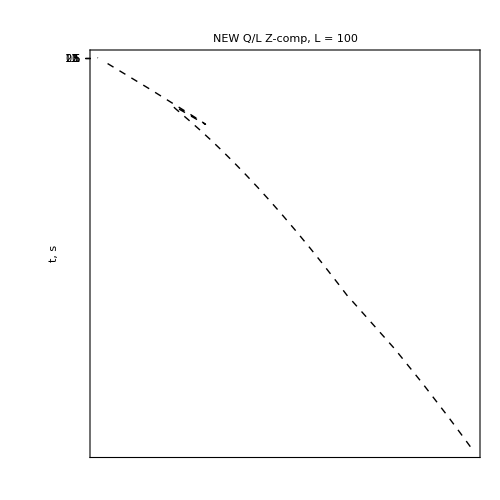
-Graphics--Graphics--Graphics- | -Graphics--Graphics--Graphics- | -Graphics--Graphics--Graphics- | -Graphics--Graphics--Graphics- | -Graphics--Graphics--Graphics-

```mathematica
a=0;
{{tlPlotSeismic[ToString@Row[{"OLD Q/L Z-comp, L = ",L[[1]]}],L100[[;;,1,;;]],freqvec,x,15,Abs@ωI,layers,depth,{.4,.8},a,50,2,"1S2PP1P"],
tlPlotSeismic[ToString@Row[{"NEW Q/L Z-comp, L = ",L[[1]]}],L100NewQ1[[;;,1,;;]],freqvec,x,15,Abs@ωI,layers,depth,{.4,.8},a,50,2,"1S2PS1P"],tlPlotSeismic[ToString@Row[{"NEW Q/L Z-comp, L = ",L[[1]]}],L100NewQ2[[;;,1,;;]],freqvec,x,15,Abs@ωI,layers,depth,{.4,.8},a,50,2,"1S2PS1P"],
tlPlotSeismic[ToString@Row[{"NEW Q/L Z-comp, L = ",L[[1]]}],L100NewQ3[[;;,1,;;]],freqvec,x,15,Abs@ωI,layers,depth,{.4,.8},a,50,2,"1S2PS1P"],
tlPlotSeismic[ToString@Row[{"NEW Q/L Z-comp, L = ",L[[1]]}],L100NewQ4[[;;,1,;;]],freqvec,x,15,Abs@ωI,layers,depth,{.4,.8},a,50,2,"1S2PS1P"]
}}//TableForm
```

```mathematica
{{tlPlotSeismic[ToString@Row[{"OLD Q/L R-comp, L = ",L[[1]]}],L100[[;;,1,;;]],freqvec,x,15,Abs@ωI,layers,depth,{.4,.8},l100R,50,2,"1S2PP1P"],
tlPlotSeismic[ToString@Row[{"NEW Q/L R-comp, L = ",L[[1]]}],L100NewQ[[;;,1,;;]],freqvec,x,15,Abs@ωI,layers,depth,{.4,.8},l100RNewQ,50,2,"1S2PS1P"]}}//TableForm
```

-Graphics--Graphics--Graphics- | -Graphics--Graphics--Graphics-